## Determine the speed c

### Mathematica simplifications

First condition

```mathematica
FullSimplify[A*(2-a)*Sqrt[c^2+4r(2(1-s)a+1)]== (1+A*(2-a))*Sqrt[c^2-4(2(1-s)(1-r+a*r)-1)] + Sqrt[c^2-4((1-s)*(1+r)-1)], r>0 && a > 0 && s > 0 && s<1]
```

(-2+a) A √(c^2+4 r-8 a r (-1+s))+(1-(-2+a) A) √(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 (r (-1+s)+s))==0

```mathematica
Assuming[ r>0 && a > 0 && s > 0 && s<1,FullSimplify[A*(2-a)*Sqrt[c^2+4r(2(1-s)a+1)]== (1+A*(2-a))*Sqrt[c^2-4(2(1-s)(1-r+a*r)-1)] + Sqrt[c^2-4((1-s)*(1+r)-1)]]]
```

(-2+a) A √(c^2+4 r-8 a r (-1+s))+(1-(-2+a) A) √(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 (r (-1+s)+s))==0

Second condition

```mathematica
FullSimplify[-c-Sqrt[c^2+4]==-  a *(1+A(2-a))*(-c+Sqrt[c^2-4*(2*(1-s)*(1-r+a*r)-1 )])- (1-a*A)*(2-a)*(-c+ Sqrt[c^2+4*r*(2 (1-s)a+1)]), r>0 && a > 0 && s > 0 && s<1]
```

(-2+a) (-1+a A) (-c+√(c^2+4 r-8 a r (-1+s)))==c+√(4+c^2)+a (-1+(-2+a) A) (-c+√(-4+c^2+8 (-1+a) r (-1+s)+8 s))

```mathematica
Assuming[ r>0 && a > 0 && s > 0 && s<1,FullSimplify[-c-Sqrt[c^2+4]==-  a *(1+A(2-a))*(-c+Sqrt[c^2-4*(2*(1-s)*(1-r+a*r)-1 )])- (1-a*A)*(2-a)*(-c+ Sqrt[c^2+4*r*(2 (1-s)a+1)])]]
```

(-2+a) (-1+a A) (-c+√(c^2+4 r-8 a r (-1+s)))==c+√(4+c^2)+a (-1+(-2+a) A) (-c+√(-4+c^2+8 (-1+a) r (-1+s)+8 s))

The simplifications made by Mathematica are not perfect. Using Assuming or FullSimplify in this case, is the same...

### Manual simplifications

First condition

```mathematica
Clear[C,c,s,r,A,a]  (*C is the squared speed*)
```

```mathematica
FullSimplify[Solve[(A*(2-a))^4 *(C + 4*r*(2*(1-s)*a+1))^2
+ (C-4((1-s)*(r+1)-1))^2+ (1+ A*(2-a))^4  (C-4*(2 (1-s)*(1-r+a*r)-1))^2-2( A*(2-a))^2 *(C + 4*r*(2*(1-s)*a+1))(C-4((1-s)*(r+1)-1))-2(C-4((1-s)*(r+1)-1))*(1+ A(2-a))^2 *(C-4*(2*(1-s)*(1-r+ a*r)-1))-2*(1+A*(2-a))^2 *(C - 4*(2*(1-s)*(1-r+a*r)-1))*(A(2-a))^2*(C + 4*r*(2*(1-s)a+1))==0,C],r>0 && a > 0 && s > 0 && s<1]
```

{{C→((1+(-3+2 a) r)^2 (-1+s)^2-4 (-2+a) A (1+(-3+2 a) r) (-1+s) (-1+2 (-1+a) r (-1+s)+2 s)-4 (-2+a)^3 A^3 (-1+2 (-1+a) r (-1+s)+2 s) (-1+r+4 a r (-1+s)+2 s-2 r s)+(-2+a)^4 A^4 (-1+r+4 a r (-1+s)+2 s-2 r s)^2+2 (-2+a)^2 A^2 (3-11 s+10 s^2+r^2 (-1+s) (-13+2 a (13+8 a (-1+s)-14 s)+14 s)+2 r (-6+(17-12 s) s+7 a (-1+s) (-1+2 s))))/((-2+a) A (-1+(-2+a) A) (-((1+(-3+2 a) r) (-1+s))+(-2+a) A (-1+r+4 a r (-1+s)+2 s-2 r s)))}}

```mathematica
s=0.46; r=1.1315789473 ;a = ( -(1-2s)*(1-r)+ Sqrt[(1-2s)^2 *(1-r)^2+8 * r^2 *(1-s)] )  /(4*r*(1-s)) ; A = (2*(1-s)*r)/(2*(1-s)*(1-r+2*a*r)-(1-r))
```

0.51961

```mathematica
((1+(-3+2 a) r)^2 (-1+s)^2-4 (-2+a) A (1+(-3+2 a) r) (-1+s) (-1+2 (-1+a) r (-1+s)+2 s)-4 (-2+a)^3 A^3 (-1+2 (-1+a) r (-1+s)+2 s) (-1+r+4 a r (-1+s)+2 s-2 r s)+(-2+a)^4 A^4 (-1+r+4 a r (-1+s)+2 s-2 r s)^2+2 (-2+a)^2 A^2 (3-11 s+10 s^2+r^2 (-1+s) (-13+2 a (13+8 a (-1+s)-14 s)+14 s)+2 r (-6+(17-12 s) s+7 a (-1+s) (-1+2 s))))/((-2+a) A (-1+(-2+a) A) (-((1+(-3+2 a) r) (-1+s))+(-2+a) A (-1+r+4 a r (-1+s)+2 s-2 r s)))    (*vitesse au carré*)
```

0.813679

```mathematica
Sqrt[%]     (*vraie vitesse, mais sans le signe*)
```

0.902042

Second condition

```mathematica
(*FullSimplify[Solve[ 3c + Sqrt[c^2+4] == (a + a*A*(2-a))*Sqrt[c^2-4*(2*(1-s)*(1-r+a*r)-1)] - (a+a*A(2-a)-2)*Sqrt[c^2+4*r*(2*(1-s)*a+1)],c], r>0 && a > 0 && s > 0 && s<1]*)
```

```mathematica
s=0.52; r=1; A = 0.48989794855663554; a =1.0206207261596576; FullSimplify[Solve[ 3c + Sqrt[c^2+4] == (a + a*A*(2-a))*Sqrt[c^2-4*(2*(1-s)*(1-r+a*r)-1)] - (a+a*A*(2-a)-2)*Sqrt[c^2+4*r*(2*(1-s)*a+1)],c]]
```

{{c→-0.0611338}}

Not the same speed....

```mathematica
FullSimplify[y''[x]+c*y'[x] + 2*(1-s)*(r*(1-y[x]-(1+atrois*Exp[csty*x] - a*y[x])) + y[x] ) - y[x] == 0]
```

2 atrois ⅇ^(csty x) r (-1+s)+y[x]+c y'[x]+y''[x]==2 s y[x]

```mathematica
FullSimplify[DSolve[{FullSimplify[%]},y[x],x]]
```

{{y[x]→(2 atrois ⅇ^(csty x) r (-1+s))/(-1-csty (c+csty)+2 (-1+a) r (-1+s)+2 s)+ⅇ^(-1/2 (c+√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) x) (C[1]+ⅇ^(√(-4+c^2+8 (-1+a) r (-1+s)+8 s) x) C[2])}}

```mathematica
Assuming[c^2>-4+8 (-1+a) r (-1+s)+8 s,FullSimplify[DSolve[{FullSimplify[y''[x]+c*y'[x] + 2*(1-s)*(r*(1-y[x]-(1+atrois*Exp[csty*x] - a*y[x])) + y[x] ) - y[x] == 0]},y[x],x]]]
```

{{y[x]→(2 atrois ⅇ^(csty x) r (-1+s))/(-1-csty (c+csty)+2 (-1+a) r (-1+s)+2 s)+ⅇ^(-1/2 (c+√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) x) (C[1]+ⅇ^(√(-4+c^2+8 (-1+a) r (-1+s)+8 s) x) C[2])}}

```mathematica
FullSimplify[DSolve[{ y''[x]+5*y'[x]+2.25*y[x]==0},y[x],x]]
```

{{y[x]→ⅇ^(-4.5 x) C[1]+ⅇ^(-0.5 x) C[2]}}

```mathematica
Assuming[a==1,DSolve[{ y''[x]-2*a*y'[x]+y[x]==0},y[x],x]]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x x C[2]}}

```mathematica
FullSimplify[((-c-Sqrt[c^2+4*r*(2*(1-s)*a+1)])/2)^2 + c*(-c-Sqrt[c^2+4*r*(2*(1-s)*a+1)])/2]
```

r-2 a r (-1+s)

```mathematica
Assuming[2*r*(1-s)*a^2+(1-2s)*(1-r)*a- r == 0,FullSimplify[(r/(1-2s(1-r)a))-(2(1-s)r/(2(1-s)(1-r+2*a*r)-1+r))]]
```

r (1/(1+2 a (-1+r) s)+(2-2 s)/(-1+r+4 a r (-1+s)+2 s-2 r s))

```mathematica
(r/(1-2s(1-r)a))-(2(1-s)r/(2(1-s)(1-r+2*a*r)-1+r))
```

-(2 r (1-s))/(-1+r+2 (1-r+2 a r) (1-s))+r/(1-2 a (1-r) s)

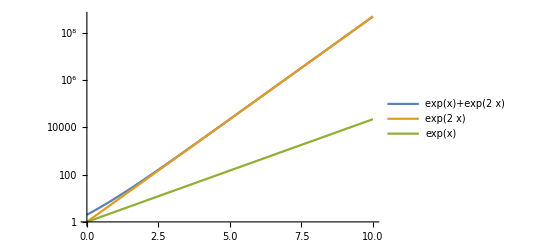

```mathematica
LogPlot[{Exp[x]+Exp[2*x],Exp[2*x],Exp[x]},{x,0,10},PlotLegends->"Expressions"]
```

System 2 : ok

```mathematica
DSolve[{nd''[x]+c*nd'[x]+((1-s)*(r+1)-1)*nd[x]==0,no''[x]+c*no'[x]-no[x]==0},{nd,no},x]
```

{{nd→Function[{x},ⅇ^(1/2 (-c-√(c^2-4 r+4 s+4 r s)) x) C[1]+ⅇ^(1/2 (-c+√(c^2-4 r+4 s+4 r s)) x) C[2]],no→Function[{x},ⅇ^(1/2 (-c-√(4+c^2)) x) C[3]+ⅇ^(1/2 (-c+√(4+c^2)) x) C[4]]}}

System 7 : complex... (understandable ; I made a choice concerning the values in exp )

```mathematica
FullSimplify[DSolve[{nd''[x]+c*nd'[x]+2*(1-s)*(r*(1-nd[x]-no[x])+nd[x])-nd[x]==0,no''[x]+c*no'[x]-r*(1-nd[x]-no[x])==0},{nd,no},x],r>0 && s > 0 && s<1]
```

{{nd→Function[{x},-(((-(2 ⅇ^(-1/2 (-c+√(-2+c^2+2 r+4 s-4 r s-2 √((-1+2 s) (1)))) x) r^2 (-1+s))/(√((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s)) √(-2+c^2+2 r+4 s-4 r s-2 √((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s))))+9+(ⅇ^(1/2 (c+√(-2+5+2 1)) x) (-r+1) (-1+3 r+2 s-2 r s+√((-1+2 s) (-1+6 r-r^2+1-4 r s+2 r^2 s))))/(√((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s)) √(-2+c^2+2 r+4 s-4 r s+2 √((-1+2 s) (-1+6+2 r^2 s))))) (1))/(2 √((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s)) √(-2+c^2+2 r+4 s-4 r s-2 √((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s))) √(-2+c^2+2 r+4 s-4 r s+2 √((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s)))))+9+(2 r (1) (ⅇ^(1/2 (-c-√(-2+5+2 √1)) x) √(-2+c^2+2 r+4 s-4 r s-2 √((-1+2 s) (-1+6+2 r^2 s)))-1-1+ⅇ^1 √1) C[4])/(√((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s)) √(-2+c^2+2 r+4 s-4 r s-2 √((-1+2 s) (1))) √(-2+c^2+2 r+4 s-4 r s+2 √((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s))))],no→Function[{x},1]}}
 |  |  |  |

Alpha Polynomial : ok

```mathematica
FullSimplify[Solve[(2*a*(1-s)*(1-r)-a-r)/(-r*(2*(1-s)*a+1)) == a , a],r>0 && s > 0 && s<1]
```

{{a→-(-1+r+√((-1+r)^2 (1-2 s)^2-8 r^2 (-1+s))+2 s-2 r s)/(4 r (-1+s))},{a→(1-r+√((-1+r)^2 (1-2 s)^2-8 r^2 (-1+s))-2 s+2 r s)/(4 r (-1+s))}}

Determine mu : ok

```mathematica
FullSimplify[Solve[ u* ((-c-Sqrt[c^2+4*r*(2*(1-s)*a+1)])/2)^2 + u*c*(-c-Sqrt[c^2+4*r*(2*(1-s)*a+1)])/2+u*(2*(1-s)* (1-r+a*r) -1) - 2*(1-s)*r*a3 ==0, u]]
```

{{u→(2 a3 r (-1+s))/(-1+r+4 a r (-1+s)+2 s-2 r s)}}

N alpha expression : ok

```mathematica
DSolve[{na''[x]+c*na'[x]- r*(2*(1-s)* a+ 1)*na[x]+ r*(2*(1-s)* a+ 1)==0},{na},x]
```

{{na→Function[{x},1+ⅇ^(1/2 (-c-√(c^2+4 r+8 a r-8 a r s)) x) C[1]+ⅇ^(1/2 (-c+√(c^2+4 r+8 a r-8 a r s)) x) C[2]]}}

```mathematica
FullSimplify[DSolve[{nd''[x]+c*nd'[x]+(2*(1-s)*(1-r+a*r)-1)*nd[x]==0},{nd},x],r>0 && s > 0 && s<1 && c^2>4(2*(1−s)*(1−r+a*r)−1)]
```

{{nd→Function[{x},ⅇ^(1/2 (-c-√(-4+c^2+8 r-8 a r+8 s-8 r s+8 a r s)) x) C[1]+ⅇ^(1/2 (-c+√(-4+c^2+8 r-8 a r+8 s-8 r s+8 a r s)) x) C[2]]}}

```mathematica
FullSimplify[DSolve[{nd''[x]+c*nd'[x]+(2*(1-s)*(1-r+a*r)-1)*nd[x]- 2*(1-s)*r*a3 *Exp[(-c-Sqrt[c^2+4*r*(2*(1-s)*a+1)])*x/2]==0 },{nd},x],r>0 && s > 0 && s<1 && c^2>4(2*(1−s)*(1−r+a*r)−1)]
```

{{nd→Function[{x},(4 a3 ⅇ^(-1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 r+8 a r-8 a r s)) x) r (-1+s) (ⅇ^(1/2 (-c+√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) x) √(-4+c^2+8 (-1+a) r (-1+s)+8 s)+ⅇ^(1/2 (-c-√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) x+1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)-√(c^2+4 r+8 a r-8 a r s)) x+1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 r+8 a r-8 a r s)) x) √(-4+c^2+8 (-1+a) r (-1+s)+8 s)-ⅇ^(1/2 (-c+√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) x) √(c^2+4 r+8 a r-8 a r s)+ⅇ^(1/2 (-c-√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) x+1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)-√(c^2+4 r+8 a r-8 a r s)) x+1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 r+8 a r-8 a r s)) x) √(c^2+4 r+8 a r-8 a r s)))/(√(-4+c^2+8 (-1+a) r (-1+s)+8 s) (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)-√(c^2+4 r+8 a r-8 a r s)) (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 r+8 a r-8 a r s)))+ⅇ^(1/2 (-c-√(-4+c^2+8 r-8 a r+8 s-8 r s+8 a r s)) x) C[1]+ⅇ^(1/2 (-c+√(-4+c^2+8 r-8 a r+8 s-8 r s+8 a r s)) x) C[2]]}}

```mathematica
r = 0.7; s=0.4
```

0.4

```mathematica
alpha = ( -(1-2s)*(1-r)+ Sqrt[(1-2s)^2 *(1-r)^2+8 * r^2 *(1-s)] )  /(4*r*(1-s))
```

1.

ALPHA VALUES

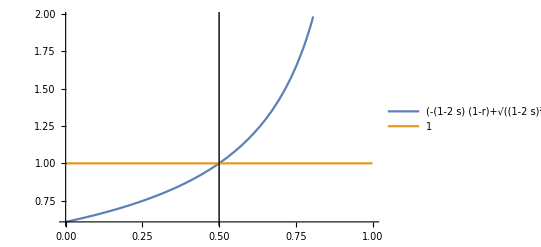

```mathematica
Plot[{( -(1-2s)*(1-r)+ Sqrt[(1-2s)^2 *(1-r)^2+8 * r^2 *(1-s)] )  /(4*r*(1-s)),1},{s,0,1},PlotLegends->"Expressions",Epilog->Line[{{0.5,0},{0.5,3}}]]
```

alpha > 1 when s > 0.5       and         alpha < 1 when s < 0.5

MINIMUM SPEED (two conditions)

```mathematica
r = 0.7
```

0.7

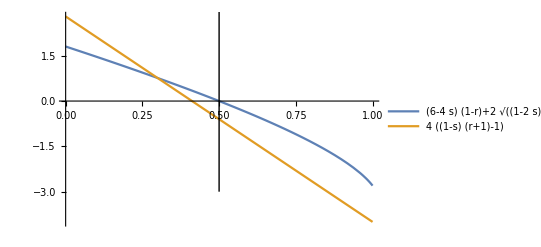

```mathematica
Plot[{(6-4s)*(1-r)+2 * Sqrt[(1-2s)^2 *(1-r)^2+8 * r^2 *(1-s)]-4,4*((1-s)*(r+1)-1)},{s,0,1},PlotLegends->"Expressions",Epilog->Line[{{0.5,3},{0.5,-3}}]]
```

```mathematica
s=0.52
```

0.52

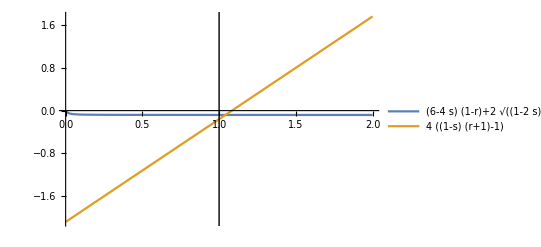

```mathematica
Plot[{(6-4s)*(1-r)+2 * Sqrt[(1-2s)^2 *(1-r)^2+8 * r^2 *(1-s)]-4,4*((1-s)*(r+1)-1)},{r,0,2},PlotLegends->"Expressions",Epilog->Line[{{1,3},{1,-3}}]]
```